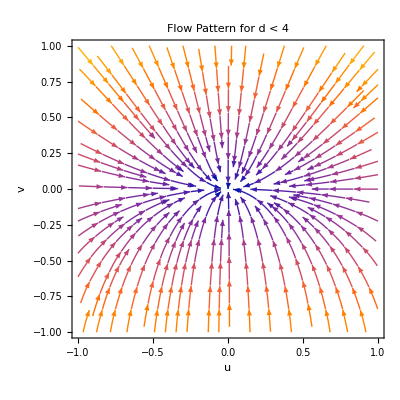

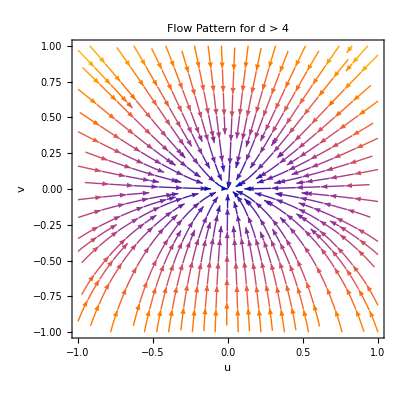

```mathematica
(*Parameters*)d1=3; (*Example for d<4*)
epsilon1=4-d1;

d2=5; (*Example for d>4*)
epsilon2=4-d2;

(*Vector field components for d<4*)
uPrime1[u_,v_]:=(epsilon1-4 (d1+8)) u-24 u v;
vPrime1[u_,v_]:=-48 v+(epsilon1-36) v;

(*Stream plot for d<4*)
StreamPlot[{uPrime1[u,v],vPrime1[u,v]},{u,-1,1},{v,-1,1},AxesLabel->{"u","v"},PlotLabel->"Flow Pattern for d < 4",StreamStyle->Red]

(*Vector field components for d>4*)
uPrime2[u_,v_]:=(epsilon2-4 (d2+8)) u-24 u v;
vPrime2[u_,v_]:=-48 v+(epsilon2-36) v;

(*Stream plot for d>4*)
StreamPlot[{uPrime2[u,v],vPrime2[u,v]},{u,-1,1},{v,-1,1},AxesLabel->{"u","v"},PlotLabel->"Flow Pattern for d > 4",StreamStyle->Blue]
```